```mathematica
snip[filename_,x_,y_,w_,h_]:=Block[{},
pageImage = ColorConvert[Import[filename],GrayLevel];
{pageWidth,pageHeight}=ImageDimensions[pageImage];
ImageTake[pageImage,{pageHeight-(y+h),pageHeight-y},{x,x+w}]
];
```

```mathematica
spec1={"/home/mg/Documents/oscillograph/page68.jpg",78,1607,1144,175};
spec2={"/home/mg/Documents/oscillograph/page69.jpg",20,1571,1145,175};
strip1=snip@@ spec1;
strip2=snip@@spec2;
strip =ImageAssemble[{strip1,strip2}]
```

-Graphics-

```mathematica
Column[Image[#,Magnification->1]& /@{strip1,strip2}]
```

-Graphics-
-Graphics-

```mathematica
Export["/home/mg/Documents/oscillograph/strip-1.png",strip1];
Export["/home/mg/Documents/oscillograph/strip-2.png",strip2];
```

```mathematica
rstrip1=ImageTake[strip1,{42,168},{30,1144}];
rstrip2=ImageTake[strip2,{42,168},{5,1139}];
Column[Image[#,Magnification->1]& /@{rstrip1,rstrip2}]
```

-Graphics-
-Graphics-

```mathematica
rstrip=ImageAssemble[{rstrip1,rstrip2}]
```

-Graphics-

```mathematica
ImageDimensions[rstrip]
```

{2250,127}

```mathematica
In the original strip, we can see some distortion that is likely due to the lossy JPEG encoding, if we adjust the contrast, brightness, and gamma.
Note the square gray "blotches" near the top.
```

```mathematica
ImageAdjust[strip1,{1,.171,.121}]
```

-Graphics-

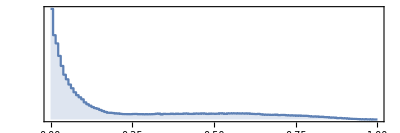

```mathematica
ImageHistogram[strip1]
```

## Appendix: Tools for Clipping and Exploring Images

Clipping strips from page images

```mathematica
Manipulate[ snip["/home/mg/Documents/oscillograph/page69.jpg",x,y,w,h], 
{{x,20}, 0, 100},{{y,1571},1500,1700},
{{w,1143},1120,1170},
{{h,178},100,200},
FrameMargins-> 0]
```

```mathematica
Manipulate[
DynamicImage[
pageImage,
 ImageSize -> {1000,1500},
Epilog->{Orange,Thickness[0.01],EdgeForm[{Thin,Orange}], FaceForm[None], Rectangle[{Dynamic[x],Dynamic[y]},{Dynamic[x]+Dynamic[w],Dynamic[y]+Dynamic[h]}]}
],
{{x,78},0,100},
{{y,1607},1500,1700},
{{w,1147},1120,1170},
{{h,175},100,200},
FrameMargins-> 0
]
```

```mathematica
ImageTake[pageImage,{1803-(1607+175),1803-1607},{78,78+1147}]
```

-Graphics-

Show JPEG artifacts by adjusting brightness, contrast, gamma

```mathematica
Manipulate[
Block[{im},
im=ImageAdjust[strip2,{b,c,g}];
List[
Image[im,Magnification->1],
ImageHistogram[im,ImageSize->Large]
]
],
{{b,1},0,1},{{c,0.171},0,1},{{g,.121},.05,2}]
```

```mathematica
Manipulate[
Block[{im},
im = ImageAdjust[rstrip2];
im=ImageAdjust[im,{b,c,g}];
im=WienerFilter[im,0.5];
List[
Image[im,Magnification->1],
ImageHistogram[im,ImageSize->Large]
]
],
{{b,1},0,1},{{c,0.171},0,1},{{g,.121},.05,2}]
```

```mathematica
try[im1_,f_]:=Block[{im},
im = ImageAdjust[im1];
im=ImageAdjust[im,{0,0,2}];
im=f[im];
List[
Image[im,Magnification->1],
ImageHistogram[im,ImageSize->Large]
]
]
```

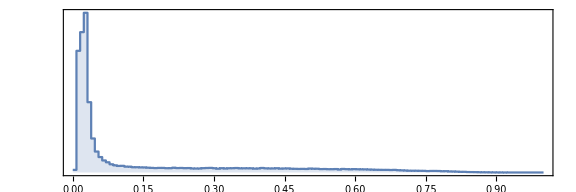
{-Graphics-,-Graphics-}

```mathematica
try[rstrip2,BilateralFilter[#,7,.1]&]
```

```mathematica
Colorize @MorphologicalComponents[ImageAdjust[rstrip2],.5]
```

-Graphics-

```mathematica
whereMax[x_]:=Position[x,Max[x]][[1]][[1]];
sigg[cols_]:=Array[whereMax[MovingAverage[cols[[#]],2]] &,Length[cols]];

astrip=ImageAdjust[rstrip,{0,0,2}];
vertStrip=Transpose[ImageData[astrip]];
signal=sigg[vertStrip];
ListPlay[signal,SampleRate->2500]
```

-Graphics-

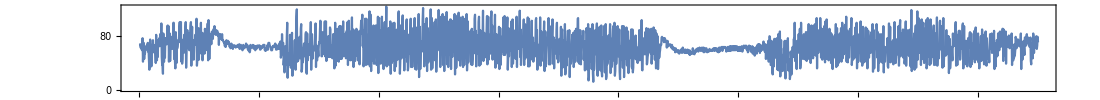

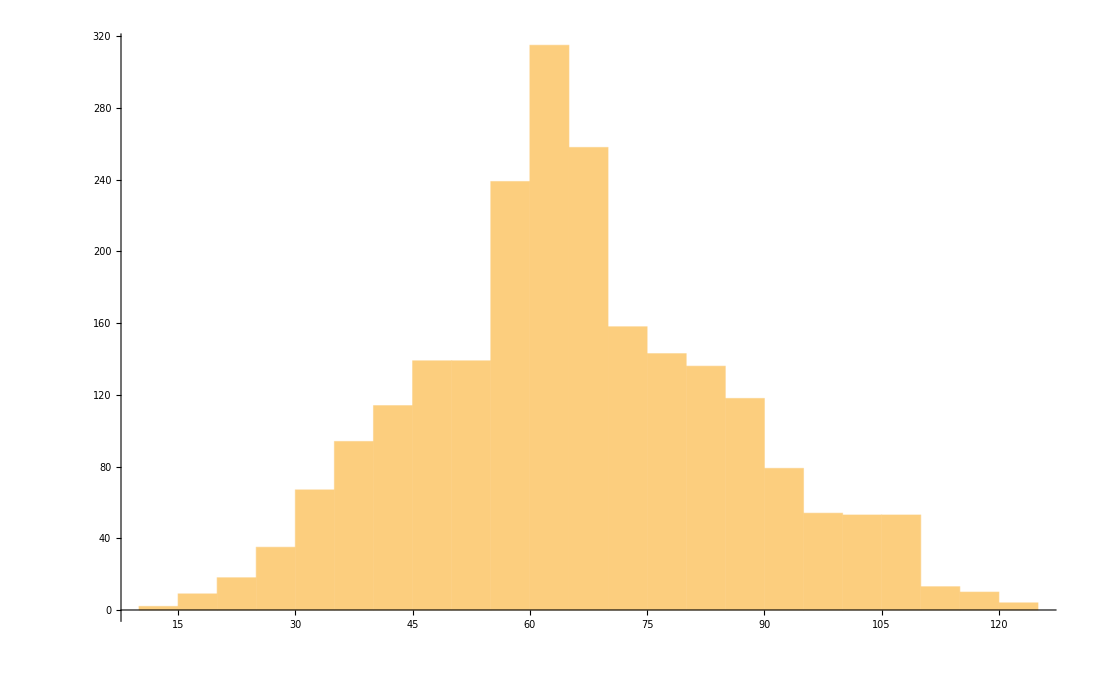

```mathematica
ListPlot[signal,ImageSize->{1100,100},Frame->True,AspectRatio->Automatic,Joined->True]
Histogram[signal]
```

```mathematica
Manipulate[
Show[
ListPlot[{MovingAverage[vertStrip[[in]],5]},PlotRange->1.0],
ListPlot[{Position[vertStrip[[in]],Max[vertStrip[[in]]]][[1]][[1]],1},PlotRange->{Length[vertStrip[[in]]],1.0}]
],
{in,1,Length[vertStrip],1}]
```

```mathematica
norm[sig_]:=Map[(# - 60)/62&, sig];
snd = Sound[SampledSoundList[norm[signal], 2500]];
Export["rstrip.wav",  snd, "WAV"]
```

rstrip.wav